```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy452-basicstatmech

Piecewise[{{1-x^(3/2), x<1}, {0, True}}]

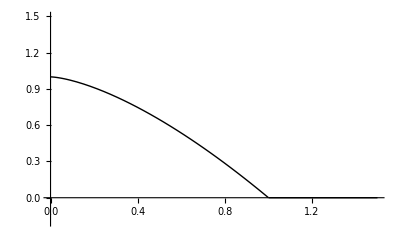

```mathematica
Clear[f]
f[x_] = Piecewise[{{1 - x^(3/2), x < 1}, {0, x≥ 1}}]
lecture20Fig2x = Plot[f[x], {x, 0, 1.5},
 PlotRange -> {{0, 1.5}, {-0.2, 1.5}},
PlotStyle->{Thick,Black},
AxesLabel->{
(*T/Subscript[T, BEC], Subscript[ρ, 0]/ρ*)
MaTeX["T/T_{\\mathrm{BEC}}"],
MaTeX["\\rho_0/\\rho"]
}
]
```

```mathematica
$Assumptions = β > 0 ;
i = Integrate[ϵ^3/(E^(ϵ β)-1), {ϵ, 0, Infinity}] ;
i // TraditionalForm
```

π^4/(15 β^4)

```mathematica
peeters`exportForLatex["lecture20Fig2x",lecture20Fig2x]
```

{lecture20Fig2x.eps,lecture20Fig2xpn.png}